```mathematica
N[Solve[{c==a ⅇ^(s/b)/.{s->1,c->50},c==a ⅇ^(s/b)/.{s->1023,c->20000}},{a,b}, Reals]]
```

{{a→49.7077,b→170.576}}

```mathematica
N[ⅇ^((s+a)/b)/.{s->1000,a->1700,b->1000}]
```

14.8797

```mathematica
Solve[ⅇ^((s+a)/b)==c,b,Reals]
```

{{b→ConditionalExpression[(a+s)/Log[c],0<c<1||c>1]}}

```mathematica
Minimize[{(a-a0)^2+((s+a)/Log[c]-b0)^2, c≥350, c≤10000,s≥0,s<1024},a]
```

{Piecewise[{{∞, !((Log[c]>0&&350≤c≤10000&&0≤s<1024)||(Log[c]<0&&350≤c≤10000&&0≤s<1024))}, {1/(1+Log[c]^2)(a0^2+2 a0 s+s^2-2 a0 b0 Log[c]-2 b0 s Log[c]+b0^2 Log[c]^2), True}}],{a→Piecewise[{{Indeterminate, !((Log[c]>0&&350≤c≤10000&&0≤s<1024)||(Log[c]<0&&350≤c≤10000&&0≤s<1024))}, {(-s+b0 Log[c]+a0 Log[c]^2)/(1+Log[c]^2), True}}]}}

```mathematica
(a-a0)^2+(b-b0)^2/.b->(a+s)/Log[c]
```

(a-a0)^2+(-b0+(a+s)/Log[c])^2

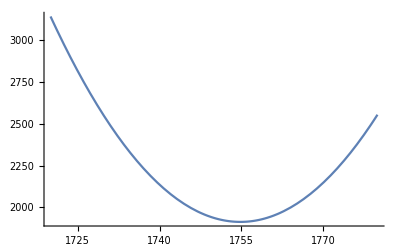

```mathematica
Plot[(a-a0)^2+((a+s)/Log[c]-b0)^2/.{s->1000,c->8000,a0->1750,b0->350},{a,1720,1780}, PlotRange->Automatic]
```

```mathematica
N[(a-a0)^2+((a+s)/Log[c]-b0)^2]/.{s->1000,c->8000,a0->1750,b0->350,a->500}
```

1.59602×10^6